```mathematica
<<ClassicalStructures.m
```

```mathematica
m=Simplify[(T[zsp[(1/3)Pi,2,0],id2[1],id2[1]].sig[2,3,1,0].T[xsp[0,2,1],xsp[0,2,1],id2[2]].sig[1,0,3,2,4,5].T[zsp[e,1,1],zsp[e,1,1],zsp[f,1,1],zsp[f,1,1],id2[2]].sig[1,0,3,2,4,5].T[xsp[0,1,2],xsp[0,1,2],id2[2]].sig[1,2,0,3].T[xsp[0,1,2],xsp[0,1,2]].sig[1,0].T[zsp[(1/3)Pi,1,1],zsp[(1/3)Pi,1,1]].xsp[0,1,2].xsp[0,2,1].sig[1,0].T[zsp[d,1,1],zsp[d,1,1]].sig[1,0].xsp[0,1,2].id2[1])]
```

{{0,0},{0,4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(ⅈ (d+f)) (1+ⅇ^(2 ⅈ e))},{0,4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(ⅈ (d+e)) (1+ⅇ^(2 ⅈ f))},{4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(ⅈ (e+f)) (1+ⅇ^(2 ⅈ d)),0}}

```mathematica
rhs=m/(4 (-1)^(1/3) (1+(-1)^(1/3)))
```

{{0,0},{0,ⅇ^(ⅈ (d+f)) (1+ⅇ^(2 ⅈ e))},{0,ⅇ^(ⅈ (d+e)) (1+ⅇ^(2 ⅈ f))},{ⅇ^(ⅈ (e+f)) (1+ⅇ^(2 ⅈ d)),0}}

```mathematica
ⅇ^(-ⅈ(d+e+f))rhs//Simplify//TeXForm
```

\left(
\begin{array}{ll}
 0 & 0 \\
 0 & e^{-i e}+e^{i e} \\
 0 & e^{-i f}+e^{i f} \\
 e^{-i d}+e^{i d} & 0
\end{array}
\right)

```mathematica
lhs=(T[zsp[c,2,0],id2[1],id2[1]].sig[1,3,2,0].T[xsp[0,1,2],xsp[0,1,2]].sig[1,0].T[zsp[a,1,1],zsp[b,1,1]].xsp[0,1,2].id2[1])//MatrixForm
```

(1+ⅇ^(ⅈ a+ⅈ b+ⅈ c) | 0
0 | ⅇ^(ⅈ b)+ⅇ^(ⅈ a+ⅈ c)
0 | ⅇ^(ⅈ a)+ⅇ^(ⅈ b+ⅈ c)
ⅇ^(ⅈ a+ⅈ b)+ⅇ^(ⅈ c) | 0)

```mathematica
Reduce[(lhs/.{c-> π-a-b})==ⅇ^(-ⅈ(d+e+f))*rhs]//Simplify
```

ⅇ^(ⅈ (2 a+2 b+d))==ⅇ^(ⅈ (a+b))+ⅇ^(ⅈ d)+ⅇ^(ⅈ (a+b+2 d))&&ⅇ^(ⅈ (2 b+e))==ⅇ^(ⅈ b)+ⅇ^(ⅈ e)+ⅇ^(ⅈ (b+2 e))&&ⅇ^(ⅈ (2 a+f))==ⅇ^(ⅈ a)+ⅇ^(ⅈ f)+ⅇ^(ⅈ (a+2 f))&&ⅇ^(ⅈ (2 a+2 b+d+e+f))≠0

```mathematica
rhs2=(T[zsp[(1/3)Pi,2,0],id2[1],id2[1]].sig[2,3,1,0].T[xsp[Pi,2,1],xsp[Pi,2,1],id2[2]].sig[1,0,3,2,4,5].T[zsp[e,1,1],zsp[-e,1,1],zsp[-f,1,1],zsp[f,1,1],id2[2]].sig[1,0,3,2,4,5].T[xsp[Pi,1,2],xsp[Pi,1,2],id2[2]].sig[1,2,0,3].T[xsp[0,1,2],xsp[0,1,2]].sig[1,0].T[zsp[(1/3)Pi,1,1],zsp[(1/3)Pi,1,1]].xsp[0,1,2].xsp[Pi,2,1].sig[1,0].T[zsp[d,1,1],zsp[-d,1,1]].sig[1,0].xsp[Pi,1,2].id2[1])//Simplify
```

{{0,0},{0,4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(-ⅈ e) (1+ⅇ^(2 ⅈ e))},{0,4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(-ⅈ f) (1+ⅇ^(2 ⅈ f))},{4 (-1)^(1/3) (1+(-1)^(1/3)) ⅇ^(-ⅈ d) (1+ⅇ^(2 ⅈ d)),0}}

```mathematica
rhs2/(8 (-1)^(1/3) (1+(-1)^(1/3)))//ExpToTrig//Simplify//TeXForm
```

\left(
\begin{array}{ll}
 0 & 0 \\
 0 & \cos (e) \\
 0 & \cos (f) \\
 \cos (d) & 0
\end{array}
\right)

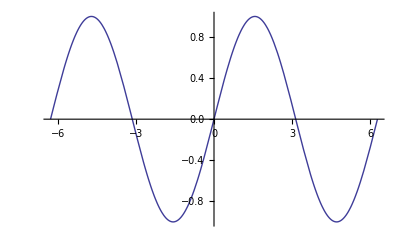

```mathematica
Plot[Cos[π/2-x],{x,-2 π,2π}]
```